En la iteracion j = 1 Obtube los valores de Xj = 1/20 f[Xj] = ⅇ^(1/400)

En la iteracion j = 2 Obtube los valores de Xj = 1/10 f[Xj] = ⅇ^(1/100)

En la iteracion j = 3 Obtube los valores de Xj = 3/20 f[Xj] = ⅇ^(9/400)

En la iteracion j = 4 Obtube los valores de Xj = 1/5 f[Xj] = ⅇ^(1/25)

En la iteracion j = 5 Obtube los valores de Xj = 1/4 f[Xj] = ⅇ^(1/16)

En la iteracion j = 6 Obtube los valores de Xj = 3/10 f[Xj] = ⅇ^(9/100)

En la iteracion j = 7 Obtube los valores de Xj = 7/20 f[Xj] = ⅇ^(49/400)

En la iteracion j = 8 Obtube los valores de Xj = 2/5 f[Xj] = ⅇ^(4/25)

En la iteracion j = 9 Obtube los valores de Xj = 9/20 f[Xj] = ⅇ^(81/400)

En la iteracion j = 10 Obtube los valores de Xj = 1/2 f[Xj] = ⅇ^(1/4)

En la iteracion j = 11 Obtube los valores de Xj = 11/20 f[Xj] = ⅇ^(121/400)

En la iteracion j = 12 Obtube los valores de Xj = 3/5 f[Xj] = ⅇ^(9/25)

En la iteracion j = 13 Obtube los valores de Xj = 13/20 f[Xj] = ⅇ^(169/400)

En la iteracion j = 14 Obtube los valores de Xj = 7/10 f[Xj] = ⅇ^(49/100)

En la iteracion j = 15 Obtube los valores de Xj = 3/4 f[Xj] = ⅇ^(9/16)

En la iteracion j = 16 Obtube los valores de Xj = 4/5 f[Xj] = ⅇ^(16/25)

En la iteracion j = 17 Obtube los valores de Xj = 17/20 f[Xj] = ⅇ^(289/400)

En la iteracion j = 18 Obtube los valores de Xj = 9/10 f[Xj] = ⅇ^(81/100)

En la iteracion j = 19 Obtube los valores de Xj = 19/20 f[Xj] = ⅇ^(361/400)

{Return[1.46378]}

Grafica con la union de trapecios :

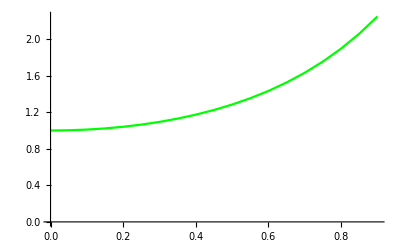

Puntos de los trapecios :

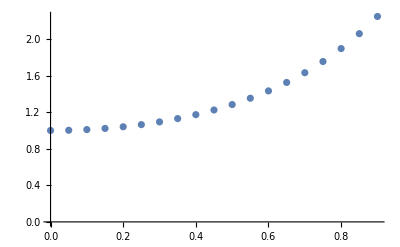

Grafica de la funcion :

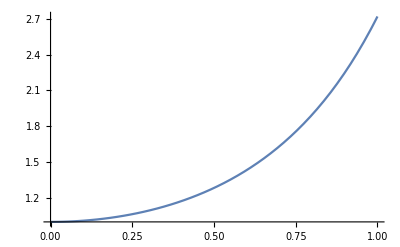

```mathematica
(* TRAPECIO 2.0 *)
f[x_] =  (*x^3 + 4 * x^2 - 10 *)   Input["Digite la funcion"] ;

a =  Input["digite el invervalo inicial: "];   
b = Input["digite el invervalo final: "];
(* f[x_] = 2/(x^2  + 4); *)
n = Input["digite el numero de subintervalos deseados: "];
(* Estas dos variables son creadas para hallar los intervalos de los trapecios y almacenar los puntos en ellas *)
coordenadas = {};
valorTrapecio = a;

MetodoTrapecio[a_, b_, n_] := {
  (* Asumiendo que 'a' es menor o igual a 'b' *)
(*Calculamos el valor de h con los datos obtenidos *)
  h = (b - a)/n;
(* Almacenamos en la variable s el valor de h medios, esto con el fin de luego añadir el resto de la formula de trapecio aquí *) 
s = h/2;
(* Creamos una variable suma que inicialmente va a contener el valor de 0, esta va a contener el valor de ∑f(xj) de la formula *)
suma = 0;
lista =
For[j = 1, j≤ (n-1), j++,
xj = a + (j * h); 
coordenada = {valorTrapecio, N[f[valorTrapecio]]};
coordenadas = Append[coordenadas, coordenada];
Print["En la iteracion j = ", j, " Obtube los valores de Xj = ", xj,  " f[Xj] = ", f[xj] ];
valorTrapecio += h;
 suma = suma + f[ xj] ;
];

(* Con todos los valores ya calculados, aplicamos la formula del trapecio *)
         s =  s* (f[a] + (2 * suma)+ f[b ]);

Return[s];
};
N[MetodoTrapecio[a, b, n]]
g1 = ListPlot[coordenadas, Joined->True, PlotStyle->RGBColor[0,1,0]];
g2 = ListPlot[coordenadas, Joined->False]; 

Print["Grafica con la union de trapecios : "];
g1

Print["Puntos de los trapecios : "];
g2 

Print["Grafica de la funcion : "];
Plot[f[x], {x,a,b}]
```